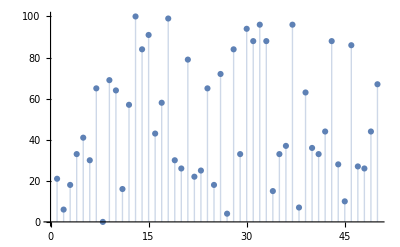

```mathematica
ns=RandomInteger[100,50];
ListPlot[ns,Filling->Axis]
```

假设最后一块（第n块）木板和第k块木板在最优解里面，则一定有min[f(n),f(x))*(n-k)]>max[(f(n),f(i))*(n-i), i in n]。
上图是不可能有这样的结果的，但是的确存在这样的情况，例如下图

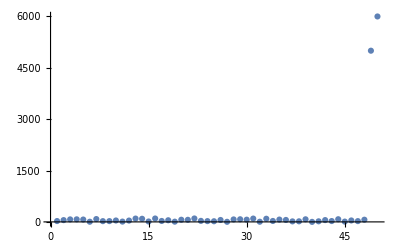

```mathematica
ListPlot[Join[RandomInteger[100,48],{5000,6000}],PlotRange->All]
```

在上图中，第1~第48块木板的长度最大为100，第49块木板的长度为5000，第50块木板的长度为6000。显然，挑选第49和第50块木板所得的容器体积为min[5000,6000]*1=5000*1=5000，而第1~48块木板能够组成的最大容器体积只有4700（当第1块木板和第48块木板都为100的时候）。所以第49和第50块木板所得的容器体积最大。所以这个问题是存在这种极端情况的，也就代表了我们的算法应该要遍历所有的木板。而对于一块木板我们要对每块木板进行计算，算出这块木板和所有其他木板组成的容器体积，这就有O(n^2)的时间复杂度了。还有更简单的算法吗？

考虑第一次遍历。

对于第一块木板来说，能够和它组成最大体积容器的那块木板应该离它足够远，并且足够高，但是这两个条件有可能不会同时满足。为了方便，我们只考虑这块木板的高度。我们可以用一个O(nlogn)的算法给所有的木板排序，这样第一块就可以用O(1)的时间找到比自己长的木板集合，和比自己短的木板集合。先考虑比自己长的木板集合，我们在比自己长的木板里找到离自己最远的木板，算出这样两块木板组成容器的体积，只需要O(1)。显然，这样就找到了这块木板和比自己长的木板的集合里面最大的容器体积，因为在这个集合里面所有的 木板都比自己长，而容器的体积取决于最短的那块板，也就是自己，所以只需要看其他木板离自己的距离就可以了。

接着我们可以思考一个问题：我们还需要考虑比自己短的木板集合吗？

答案是否定的

因为对于一个最优解来说，一定有一个长木板和短木板（不妨设两块木板相等长度时靠左的那块更长），而我们上述的办法对于所有木板都考虑了所有比自己长的木板，所以我们一定会经过最优解。这样，我们就解决了问题。

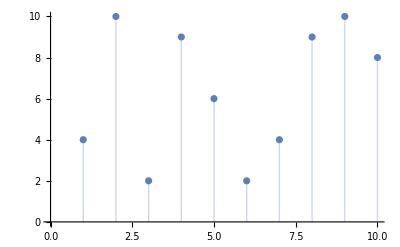

```mathematica
numPlanks=10;
largestLength=10;
planks=Table[{i,RandomInteger[largestLength]},{i,1,numPlanks}];
(*作图*)
Show[ListPlot[planks,Filling->Axis]]
```

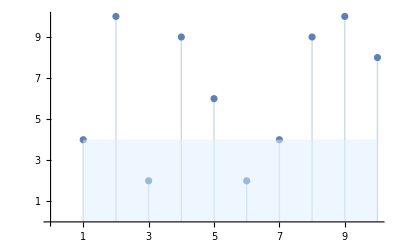

```mathematica
pic1=Show[ListPlot[planks,Filling->Axis,Ticks->{Range[10],Range[10], Automatic}],Graphics[Style[Rectangle[{1,0},{10,4}],LightBlue,Opacity[0.5]]]]
```

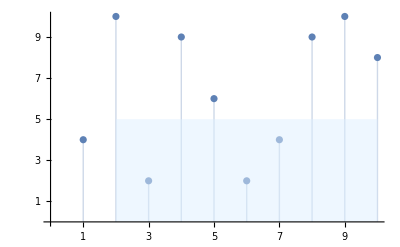

```mathematica
pic2=Show[ListPlot[planks,Filling->Axis,Ticks->{Range[10],Range[10], Automatic}],Graphics[Style[Rectangle[{2,0},{10,5}],LightBlue,Opacity[0.5]]]]
```

```mathematica
LargestContainer[Planks_]:=
(sortedPlanks=Reverse[SortBy[Planks,Last]];   (*按照木板长度从小到大排序*)
maxV=0;
bestCombo={};
For[i=1,i<Length[sortedPlanks],i++,(
farthestPlankIdx=Max[sortedPlanks[[i+1;;numPlanks,1]]];
(*Print[farthestPlankIdx];*)
V=sortedPlanks[[i,2]]*Planks[[farthestPlankIdx,2]];(*取比自己长的最远木板*)
If[V≥maxV,(maxV=V;bestCombo={i,farthestPlankIdx};),Null];
)];
Return[{maxV,bestCombo}];
)
```

```mathematica
LargestContainer[planks]
```

{80,{2,10}}

```mathematica
planks
```

{{1,4},{2,10},{3,2},{4,9},{5,6},{6,2},{7,4},{8,9},{9,10},{10,8}}

```mathematica
tblPlanks=Table[{i,j,1},{i,10},{j,10}]
```

{{{1,1,1},{1,2,1},{1,3,1},{1,4,1},{1,5,1},{1,6,1},{1,7,1},{1,8,1},{1,9,1},{1,10,1}},{{2,1,1},{2,2,1},{2,3,1},{2,4,1},{2,5,1},{2,6,1},{2,7,1},{2,8,1},{2,9,1},{2,10,1}},{{3,1,1},{3,2,1},{3,3,1},{3,4,1},{3,5,1},{3,6,1},{3,7,1},{3,8,1},{3,9,1},{3,10,1}},{{4,1,1},{4,2,1},{4,3,1},{4,4,1},{4,5,1},{4,6,1},{4,7,1},{4,8,1},{4,9,1},{4,10,1}},{{5,1,1},{5,2,1},{5,3,1},{5,4,1},{5,5,1},{5,6,1},{5,7,1},{5,8,1},{5,9,1},{5,10,1}},{{6,1,1},{6,2,1},{6,3,1},{6,4,1},{6,5,1},{6,6,1},{6,7,1},{6,8,1},{6,9,1},{6,10,1}},{{7,1,1},{7,2,1},{7,3,1},{7,4,1},{7,5,1},{7,6,1},{7,7,1},{7,8,1},{7,9,1},{7,10,1}},{{8,1,1},{8,2,1},{8,3,1},{8,4,1},{8,5,1},{8,6,1},{8,7,1},{8,8,1},{8,9,1},{8,10,1}},{{9,1,1},{9,2,1},{9,3,1},{9,4,1},{9,5,1},{9,6,1},{9,7,1},{9,8,1},{9,9,1},{9,10,1}},{{10,1,1},{10,2,1},{10,3,1},{10,4,1},{10,5,1},{10,6,1},{10,7,1},{10,8,1},{10,9,1},{10,10,1}}}

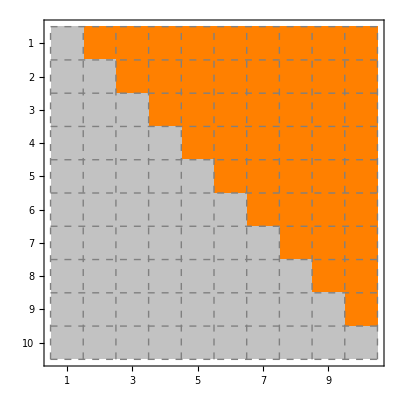

```mathematica
MatrixPlot[Table[{Boole[i>=1],Boole[i>=2],Boole[i>=3],Boole[i≥4],Boole[i≥5],Boole[i≥6],Boole[i≥7],Boole[i≥8],Boole[i≥9],Boole[i≥10]},{i,10}],Mesh->All,MeshStyle->Directive[Gray,Dashed],ColorRules->{1->GrayLevel[0.76],0->Orange}]
```

```mathematica
a=0.2;t=2;
```

```mathematica
piec[x_,top_,btm_]:=
Piecewise[{{btm,x≤btm},{x,x<top&&x>btm},{top,x≥top}}]
```

```mathematica
step[x_,n_]:=
Piecewise[{{0,x==0},{n,x>0}}]
```

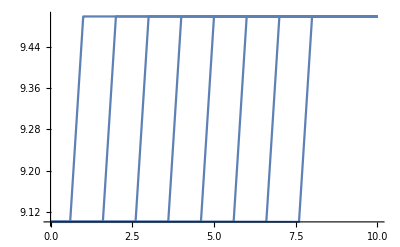

```mathematica
Plot[Table[piec[j+x,9.5,9.1],{j,1.5,8.5,1}],{x,0,10}]
```

```mathematica
piecLine[a_,b_,c_,d_]:=
Piecewise[{{Null,a==c&&b==d},{Line[{{a,b},{c,d}}],a≠c||b≠d}}]
```

```mathematica
rowCrosses[startX_,offset_,num_,startT_,rowNum_]:=
Table[Graphics[{AbsoluteThickness[t],
piecLine[startX-a,10.5-rowNum+a,piec[k]]}]]
```

```mathematica
Manipulate[Show[MatrixPlot[Table[{Boole[i>=1],Boole[i>=2],Boole[i>=3],Boole[i≥4],Boole[i≥5],Boole[i≥6],Boole[i≥7],Boole[i≥8],Boole[i≥9],Boole[i≥10]},{i,10}],Mesh->All,MeshStyle->Directive[Gray,Dashed],ColorRules->{1->GrayLevel[0.76],0->Orange}],
Table[Graphics[{AbsoluteThickness[t],piecLine[j-a,9.5-a,piec[k,j+a,j-a],piec[-j+k+9.5,9.5+a,9.5-a]],piecLine[j-a,9.5+a,piec[k,j+a,j-a],piec[9.5+j-k,9.5+a,9.5-a]]}],{j,1.5,8.5,1}],   (*first row*)


Table[Graphics[{AbsoluteThickness[t],piecLine[9.5-a,j-a,piec[-j+k+9.5,9.5+a,9.5-a],piec[k,j+a,j-a]]}],{j,7.5,1.5,-1}],
Table[
Graphics[{AbsoluteThickness[t],
piecLine[9.5-a,j+a,9.5-a+piec[k-j-0.5+a,2a,0],j+a-piec[k-j-0.5+a,2a,0]]}],{j,1.5,7.5,1}],

Table[Graphics[{AbsoluteThickness[t],
piecLine[j+1-a,8.5+a,piec[k-11.5+2.5,j+1+a,j+1-a],piec[20-k+j-1.5,8.5+a,8.5-a]],
piecLine[j+1-a,8.5-a,piec[k-11.5+2.5,j+1+a,j+1-a],piec[k-11.5+8.5-j+1.5,8.5+a,8.5-a]]}],{j,1.5,6.5,1}],
(*Graphics[{AbsoluteThickness[t],piecLine[2.5-a,8.5+a,piec[k-11.5+2.5,2.5+a,2.5-a],piec[20-k,8.5+a,8.5-a]]}],
Graphics[{AbsoluteThickness[t],piecLine[3.5-a,8.5+a,piec[k-11.5+2.5,3.5+a,3.5-a],piec[20-k+1,8.5+a,8.5-a]]}],
Graphics[{AbsoluteThickness[t],piecLine[4.5-a,8.5+a,piec[k-11.5+2.5,4.5+a,4.5-a],piec[20-k+2,8.5+a,8.5-a]]}],*)

(*Graphics[{AbsoluteThickness[t],
piecLine[2.5-a,8.5-a,piec[k-11.5+2.5,2.5+a,2.5-a],piec[k-11.5+8.5,8.5+a,8.5-a]]}],
Graphics[{AbsoluteThickness[t],
piecLine[3.5-a,8.5-a,piec[k-11.5+2.5,3.5+a,3.5-a],piec[k-11.5+8.5-1,8.5+a,8.5-a]]}],*)

Graphics[{AbsoluteThickness[t],Circle[{9.5,9.5},1.3a,{0,piec[k,2,0]Pi}]}],
Graphics[{AbsoluteThickness[t],Circle[{9.5,8.5},1.3a,{0,piec[k-4,2,0]Pi}]}],
Graphics[{AbsoluteThickness[t],Circle[{8.5,8.5},1.3a,{0,piec[k-6,2,0]Pi}]}],
Graphics[{AbsoluteThickness[t],Circle[{7.5,7.5},1.3a,{0,piec[k-8,2,0]Pi}]}]
],{k,0,20}]
```

```mathematica
Table[{{piec[j,(j-0.5)2]-a,9.5-a},{piec[j,(j-0.5)2]+a,9.5+a}},{j,1.5,8.5,1}]
```

{{{-0.2+piec[1.5,2.],9.3},{0.2+piec[1.5,2.],9.7}},{{-0.2+piec[2.5,4.],9.3},{0.2+piec[2.5,4.],9.7}},{{-0.2+piec[3.5,6.],9.3},{0.2+piec[3.5,6.],9.7}},{{-0.2+piec[4.5,8.],9.3},{0.2+piec[4.5,8.],9.7}},{{-0.2+piec[5.5,10.],9.3},{0.2+piec[5.5,10.],9.7}},{{-0.2+piec[6.5,12.],9.3},{0.2+piec[6.5,12.],9.7}},{{-0.2+piec[7.5,14.],9.3},{0.2+piec[7.5,14.],9.7}},{{-0.2+piec[8.5,16.],9.3},{0.2+piec[8.5,16.],9.7}}}

```mathematica
Grid[Table[o,{4},{7}],Frame->All,FrameStyle->Dashing[Tiny]]
```

o | o | o | o | o | o | o
o | o | o | o | o | o | o
o | o | o | o | o | o | o
o | o | o | o | o | o | o

```mathematica
cross[x_,y_,r_]:=
{Line[{{x-r,y-r},{x+r,y+r}}],Line[{{x-r,y+r},{x+r,y-r}}]}
```

```mathematica
g = Manipulate[Show[MatrixPlot[Table[{Boole[i>=1],Boole[i>=2],Boole[i>=3],Boole[i≥4],Boole[i≥5],Boole[i≥6],Boole[i≥7],Boole[i≥8],Boole[i≥9],Boole[i≥10]},{i,10}],Mesh->All,MeshStyle->Directive[Gray,Dashed],ColorRules->{1->GrayLevel[0.76],0->Orange}],
Graphics[Table[cross[j,]]]

Graphics[{AbsoluteThickness[t],Circle[{9.5,9.5},1.3a,{0,piec[k,2,0]Pi}]}],
Graphics[{AbsoluteThickness[t],Circle[{9.5,8.5},1.3a,{0,piec[k-4,2,0]Pi}]}],
Graphics[{AbsoluteThickness[t],Circle[{8.5,8.5},1.3a,{0,piec[k-6,2,0]Pi}]}],
Graphics[{AbsoluteThickness[t],Circle[{7.5,7.5},1.3a,{0,piec[k-8,2,0]Pi}]}]
],{k,0,20}];
```

```mathematica
SetDirectory@NotebookDirectory[];
Export["container.gif",g];
```